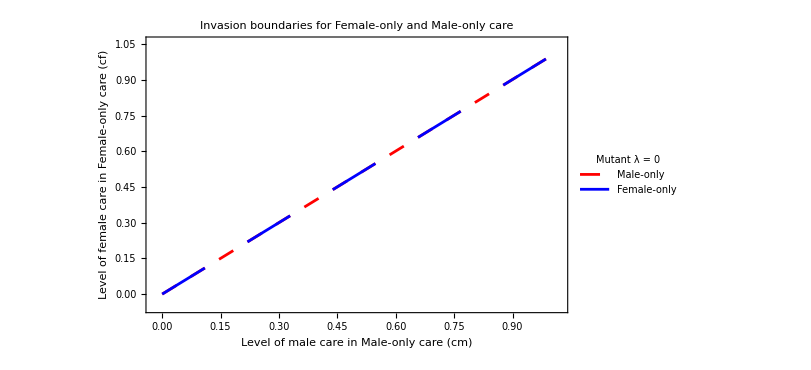

```mathematica
(*26th February 2024 - Simplifying code so it just plots the invasion boundary*)

(*BASELINES*)
em0=0.393;
ef0 = 1-em0;
mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;

z0=1;
(*_________________________________________________________________________*)
(*RESIDENT strategies*)


(*Male only care*)
emres=em0;
efres =1-emres;

zres = z0;
(*cmres = 0.7;*)
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
wmres=1-((1-wm0)*E^(-cmres));
wfres= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres)));

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;

AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));




(*Female only*)
emres2=em0;
efres2 =1-emres2;

zres = z0;
cmres2 = 0.0;
(*cfres2 = 0.7;*)
ctres2 = cmres2+cfres2;

mumres2=mum0*E^(-zres*ctres2);
mufres2=muf0*E^(-zres*ctres2);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres2=1-((1-mm0)*E^(-((1-mum0)*emres2)));
mfres2=1-((1-mf0)*E^(-((1-muf0)*efres2)));
KR2=k0;
rres2=rr0*E^(-((1-mum0)*emres2+((1-muf0)*efres2))/2);

wmres2=1-((1-wm0)*E^(-cmres2));
wfres2= 1-((1-wf0)*E^(-(efres2*(1-muf0)+(1-mum0)*emres2+cfres2)));

emmres2 = emres2*(1-mumres2)*mmres2;
emfres2 = efres2* (1-mufres2)*mfres2;
esmres2= emres2*(1-mumres2);
esfres2 = efres2* (1-mufres2);
amres2 = emres2*(1-mumres2)*mmres2*sigjmres;
afres2 = efres2* (1-mufres2)* mfres2*sigjfres;

AR2 =KR2*(1-((wmres2*amres2+wfres2*afres2)*(mumres2*emres2 + mufres2*efres2 + mmres2*esmres2 + mfres2*esfres2)/((emmres2*sigjmres+emfres2*sigjfres)*rres2*afres2)));



(*___________________________________________________*)
(*MUTANT strategies*)


(*Male only care*)
z=z0;
(*cm4=0.7;*)
cf4=0.0;
ct4 = cm4 + cf4;

mum4=mum0*E^(-z*ct4);
muf4=muf0*E^(-z*ct4);

em4=em0;
ef4 = 1-em4;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm4=1-((1-mm0)*E^(-((1-mum0)*em4)));
mf4=1-((1-mf0)*E^(-((1-muf0)*ef4)));
k4=k0; 
rr4=rr0*E^(-((1-mum0)*em4+((1-muf0)*ef4))/2);

wm4=1-((1-wm0)*E^(-cm4));
wf4=1-((1-wf0)*E^(-(ef4*(1-muf0)+(1-mum0)*em4 +cf4)));

emm4 = em4*(1-mum4)*mm4;
emf4 = ef4* (1-muf4)*mf4;
esm4= em4*(1-mum4);
esf4 = ef4*(1-muf4);
am4 = em4*(1-mum4)*mm4*sigjm;
af4= ef4* (1-muf4)* mf4*sigjf;



(*Female only care*)
z=z0;
cm2=0.0;
(*cf2=0.7;*)
ct2 = cm2 + cf2;
ct2;
em2=em0;
ef2 = 1-em2;

mum2=mum0*E^(-z*ct2);
muf2=muf0*E^(-z*ct2);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm2=1-((1-mm0)*E^(-((1-mum0)*em2)));
mf2=1-((1-mf0)*E^(-((1-muf0)*ef2)));

k=k0;
rr2=rr0*E^(-((1-mum0)*em2+((1-muf0)*ef2))/2);

wm2=1-((1-wm0)*E^(-cm2));
wf2=1-((1-wf0)*E^(-(ef2*(1-muf0)+(1-mum0)*em2 +cf2)));

emm2 = em2*(1-mum2)*mm2;
emf2 = ef2* (1-muf2)*mf2;
esm2 = em2*(1-mum2);
esf2 = ef2*(1-muf2);
am2 = em2*(1-mum2)*mm2*sigjm;
af2 = ef2* (1-muf2)* mf2*sigjf;



(*INVASION MATRICIES*)

(*Invading MALE only care resident*)
      (*Female only care mutant*)
a2=-(mum2*em2+muf2*ef2+mm2*esm2+mf2*esf2);
b2 = rr2*af2*(1-(AR/k));
c2=emm2*sigjm*(1-ϕ*taum)+emf2*sigjf*(1-ϕ*tauf);
d2 = -(wm2*am2+wf2*af2);
mat20={{-ϕ+a2,b2},{c2,-ϕ+d2}};
MatrixForm[mat20];
ans20=Solve[Det[mat20]==0,ϕ];
res20 = Max[ϕ/.ans20];


(*Invading FEMALE only care resident*)
         (*Male only care mutant*)
a=-(mum4*em4+muf4*ef4+mm4*esm4+mf4*esf4);
b02 = rr4*af4*(1-(AR2/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat02={{-λ+a,b02},{c,-λ+d}};
MatrixForm[mat02];
ans02=Solve[Det[mat02]==0,λ];
res02=Max[λ/.ans02];



(**BOUNDARIES, using root solving**)

(*Male only(M) invades(i) Female only(F)*)
resMiF=Table[cm4=0.0+i/10;jo=
FindRoot[{res02==0},{cfres2,0.4,0.6}];{cm4, cfres2/.jo},{i,0,10}];



(*Female only (F) invades(i) Male only(M), Flipped to have the same axes as MiF*)

resFiMflip=Table[cmres=0.0+i/10;jo=
FindRoot[{res20==0},{cf2,0.4,0.6}];{ cmres, cf2/.jo},{i,0,10}];


(**PLOTS**)
(*Combined plot*)
ListPlot[{Re[resMiF],Re[resFiMflip]},
Joined -> {True, True},
Frame -> {True,True, False, False},
PlotLegends->LineLegend[{"Male-only", "Female-only"},
LegendLabel-> "Mutant λ = 0" ,
LegendMarkerSize->{20,20},
LabelStyle ->{FontSize->16}
],
FrameLabel->{Style["Level of male care in Male-only care (cm)",16],Style[Rotate[Column[{"Level of female care in","Female-only care" ,"(cf)  "},Alignment-> Center], 270 Degree],16]},
PlotLabel->Style[ Column[{"Invasion boundaries for Female-only and Male-only care", ""}],18],LabelingSize->350,LabelStyle->Black,
ImageSize-> 600,
PlotStyle  -> {{Red, Dashing[0.02]}, {Blue, Dashing[0.06]}},
BaseStyle-> {FontSize-> 14}]
```